```mathematica
<<QI`
```

```mathematica
(*The Unknown Target State*)
```

```mathematica
Subscript[ρ, β][p0_,p1_,p2_]=DiagonalMatrix[{p0,p1,p2}];
```

```mathematica
(*The Estimates one obtains by running our protocol with access to a qubit probe.*)
```

```mathematica
Subscript[ω, 0][p0_,p1_,p2_]=DiagonalMatrix[{p0,(p1+p2)/2,(p1+p2)/2}];
Subscript[ω, 1][p0_,p1_,p2_]=DiagonalMatrix[{(p0+p2)/2,p1,(p0+p2)/2}];
Subscript[ω, 2][p0_,p1_,p2_]=DiagonalMatrix[{(p0+p1)/2,(p0+p1)/2,p2}];
```

```mathematica
(*Symmetrised Estimate State*)
```

```mathematica
Symmetrised[p0_,p1_,p2_] =(1/2)*(Subscript[ρ, β][p0,p1,p2]+IdentityMatrix[3]/3);
```

```mathematica
(*Function to convert Lexicographic ordering to computational basis*)
```

```mathematica
LexToNum[i_,j_,k_]=9*i+3*k+j+1;
(*Basis Ket Generator and Hamming Weight Distant GHZ Like Subspaces Generator*)
BasisKet[i_]:=IdentityMatrix[27][[i]]
Subspace[k_,l_]:=Table[BasisKet[LexToNum[j,Mod[k+j,3],Mod[l+j,3]]],{j,0,2}];
```

```mathematica
(*Product of Estimate States*)
```

```mathematica
(*Switcheroo*)
```

```mathematica
OmegaBar[p0_,p1_,p2_] = KroneckerProduct[Subscript[ω, 0][p0,p1,p2],Subscript[ω, 1][p0,p1,p2],Subscript[ω, 2][p0,p1,p2]];
(*Sort the vector of eigenvalues for a given choice of values*)
Sorted[p0_,p1_,p2_] := Sort[Diagonal[OmegaBar[p0,p1,p2]],Greater];
OmegaBarDesc[p0_,p1_,p2_]:=DiagonalMatrix[Sorted[p0,p1,p2]];
```

```mathematica
(*Construct Marginal For a given Choice of Values with Global Sorting*)
```

```mathematica
MarginalDesc[p0_,p1_,p2_]:=PartialTrace[OmegaBarDesc[p0, p1, p2], 3, 9, 2]
MarginalDescSums[p0_,p1_,p2_]:={Diagonal[MarginalDesc[p0,p1,p2]][[1]],Diagonal[MarginalDesc[p0,p1,p2]][[1]]+Diagonal[MarginalDesc[p0,p1,p2]][[2]],Total[Diagonal[MarginalDesc[p0,p1,p2]]]}
```

```mathematica
(*Let's check when a given qutrit target state will have estimate states which allow for reconstruction i.e. satisfy the majorisation condition*)
```

```mathematica
Ineq[p0_,p1_,p2_]:={MarginalDescSums[p0,p1,p2][[1]]>=p0,MarginalDescSums[p0,p1,p2][[2]]>=p0 + p1};
```

```mathematica
True[Ineq[3/6,2/6,1/6]]
```

True[{True,True}]

```mathematica
(*Let's check for an equally spaced hamiltonian*)
```

```mathematica
MarginalKet[i_]:=IdentityMatrix[3][[i]]
```

```mathematica
MarginalProj[i_]:=Outer[Times,MarginalKet[i],MarginalKet[i]]
```

```mathematica
H[E0_,E1_,E2_] =E0*MarginalProj[1]+E1*MarginalProj[2]+E2*MarginalProj[3]
```

```mathematica
ThermalPops[β_,E0_,E1_,E2_] = Diagonal[MatrixExp[-β*H[E0,E1,E2]]/Tr[MatrixExp[-β*H[E0,E1,E2]]]];
```

```mathematica
(*Globally Sorted Inequality 1*)
```

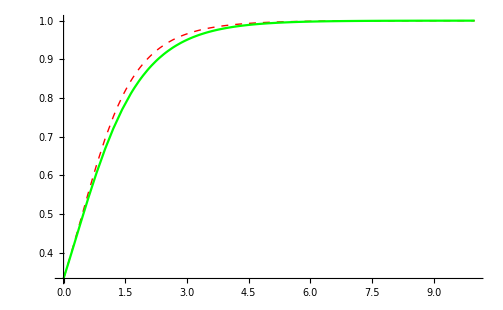

```mathematica
Plot[{Diagonal[MarginalDesc[ThermalPops[β,0,1,2][[1]],ThermalPops[β,0,1,2][[2]],ThermalPops[β,0,1,2][[3]]]][[1]],ThermalPops[β,0,1,2][[1]]},{β,0,10},PlotStyle->{{Red,Dashed,Thick},{Green}},PlotRange->All]
```

```mathematica
(*Global Sorting Inequality 2*)
```

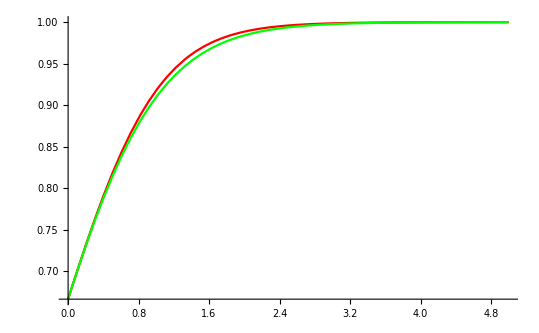

```mathematica
Plot[{Diagonal[MarginalDesc[ThermalPops[β,0,1,2][[1]],ThermalPops[β,0,1,2][[2]],ThermalPops[β,0,1,2][[3]]]][[1]]+Diagonal[MarginalDesc[ThermalPops[β,0,1,2][[1]],ThermalPops[β,0,1,2][[2]],ThermalPops[β,0,1,2][[3]]]][[2]],ThermalPops[β,0,1,2][[1]]+ThermalPops[β,0,1,2][[2]]},{β,0,5},PlotStyle->{Red,Green},PlotRange->All]
```

```mathematica
(*Very cool there should exist a Bistochastic Matrix which when applied to each subspace gives us this transformation - Let's now construct the subspaces and find this Bistochastic Matrix*)
```

```mathematica
(*Vectors of Populations in Each of the Subspaces*)
```

```mathematica
RVec[k_,l_,p0_,p1_,p2_]:=Table[ConjugateTranspose[Subspace[k,l][[j]]].OmegaBarDesc[p0,p1,p2].Subspace[k,l][[j]],{j,1,3}]
```

```mathematica
AllRVecs[p0_,p1_,p2_] := {RVec[0,0,p0,p1,p2],RVec[0,1,p0,p1,p2],RVec[0,2,p0,p1,p2],RVec[1,0,p0,p1,p2],RVec[2,0,p0,p1,p2],RVec[1,1,p0,p1,p2],RVec[1,2,p0,p1,p2],RVec[2,1,p0,p1,p2],RVec[2,2,p0,p1,p2]};
```

```mathematica
(*The 6 3X3 Permutation Matrices*)
```

```mathematica
PM[l_]:=PermutationMatrix[Permutations[{1,2,3}][[l]]]
```

```mathematica
(*A Bistochastic Matrix is a convex mixture of permutation matrices*)
```

```mathematica
BiStoch[a0_,a1_,a2_,a3_,a4_,a5_]=FullSimplify[a0*PM[1]+a1*PM[2]+a2*PM[3]+a3*PM[4]+a4*PM[5]+a5*PM[6],{a0+a1+a2+a3+a4+a5+a6==1,a0>=0,a1>=0,a2>=0,a3>=0,a4>=0,a5>=0}]
```

{{a0+a1,a2+a3,a4+a5},{a2+a4,a0+a5,a1+a3},{a3+a5,a1+a4,a0+a2}}

```mathematica
{{a0+a1,a2+a3,a4+a5},{a2+a4,a0+a5,a1+a3},{a3+a5,a1+a4,a0+a2}}//MatrixForm
```

(a0+a1 | a2+a3 | a4+a5
a2+a4 | a0+a5 | a1+a3
a3+a5 | a1+a4 | a0+a2)

```mathematica
(*Bistochastic Matrix Applied to the sum of the population vectors*)
```

```mathematica
FirstEntryMarginal[a0_,a1_,a2_,a3_,a4_,a5_,p0_,p1_,p2_] := Total[Flatten[Table[(BiStoch[a0,a1,a2,a3,a4,a5].RVec[k,l,p0,p1,p2])[[1]],{k,0,2},{l,0,2}]]];
SecondEntryMarginal[a0_,a1_,a2_,a3_,a4_,a5_,p0_,p1_,p2_] := Total[Flatten[Table[(BiStoch[a0,a1,a2,a3,a4,a5].RVec[k,l,p0,p1,p2])[[2]],{k,0,2},{l,0,2}]]];
ThirdEntryMarginal[a0_,a1_,a2_,a3_,a4_,a5_,p0_,p1_,p2_] := Total[Flatten[Table[(BiStoch[a0,a1,a2,a3,a4,a5].RVec[k,l,p0,p1,p2])[[3]],{k,0,2},{l,0,2}]]];
```

```mathematica
(*Equations for a given set of values fixed with the sorting fixed*)
```

```mathematica
EquationsNum[p0_,p1_,p2_]:=FirstEntryMarginal[a0,a1,a2,a3,a4,a5,p0,p1,p2]==p0&&SecondEntryMarginal[a0,a1,a2,a3,a4,a5,p0,p1,p2]==p1&&ThirdEntryMarginal[a0,a1,a2,a3,a4,a5,p0,p1,p2]==p2&&a0+a1+a2+a3+a4+a5==1&&a0>=0&&a1>=0&&a2>=0&&a3>=0&&a4>=0 &&a5>=0;
```

```mathematica
(*Let's see if there's a Bistchochastic Matrix for the example Subscript[ρ, β]={3/6,2/6,1/6} we chose earlier*)
```

```mathematica
FindInstance[EquationsNum[3/6,2/6,1/6],{a0,a1,a2,a3,a4,a5},Reals,3]
```

{{a0→9/10,a1→0,a2→1/10,a3→0,a4→0,a5→0}}

```mathematica
B1=BiStoch[9/10,0,1/10,0,0,0]
```

{{9/10,1/10,0},{1/10,9/10,0},{0,0,1}}

```mathematica
{{9/10,1/10,0},{1/10,9/10,0},{0,0,1}}//MatrixForm
```

(9/10 | 1/10 | 0
1/10 | 9/10 | 0
0 | 0 | 1)

```mathematica
AllRVecs[p0_,p1_,p2_] := {RVec[0,0,p0,p1,p2],RVec[0,1,p0,p1,p2],RVec[0,2,p0,p1,p2],RVec[1,0,p0,p1,p2],RVec[2,0,p0,p1,p2],RVec[1,1,p0,p1,p2],RVec[1,2,p0,p1,p2],RVec[2,1,p0,p1,p2],RVec[2,2,p0,p1,p2]};
```

```mathematica
Total[Table[B1.AllRVecs[3/6,2/6,1/6][[j]],{j,1,9}]]
```

{1/2,1/3,1/6}